```mathematica
Clear["Global`*"];
```

```mathematica
A=({{-b/J, K/J}, {-K/L, -R/L}});
```

```mathematica
f[x_,y_] :=A.{x,y}+{0,V/L}
```

```mathematica
J=0.00027238;
b=0.0812;
K=0.1079;
R=0.4425;
L=0.0038;
V=5;
```

```mathematica
f[x,y]
```

{-10. x+5.22222 y,1315.79-12.3684 x-623.684 y}

```mathematica
c1=0; c2=0; (*intitial values*)
```

```mathematica
t0=0; T=5;  h=0.0001; n=(T-t0)/h; (*t0: intitial time, T: end of time, h: stepsize, n: number of steps*)
X=Table[t0+h i,{i,0,n}];  (*gridpoints: time*)
Y=Table[0,{i,1,2},{j,1,n+1}];  (*gridpoints: x,y*)
Y[[All,1]]={c1,c2}; (*gridpoints: x,y*)
```

{1.09044,2.08808}

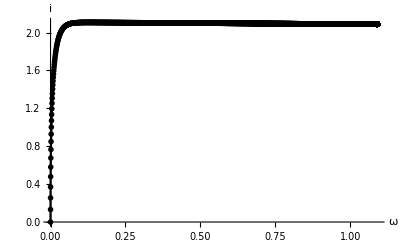

```mathematica
For[i=1,i≤n,i++,
Y[[All,i+1]]=Y[[All,i]]+h f[Y[[1,i]],Y[[2,i]]]
]
Y[[All,n+1]]
ListPlot[Table[{Y[[1,i]],Y[[2,i]]},{i,1,n+1}],PlotRange->Full,Mesh->Full, Joined->True,AxesLabel->{"ω","i"},PlotTheme->"Monochrome"]
```

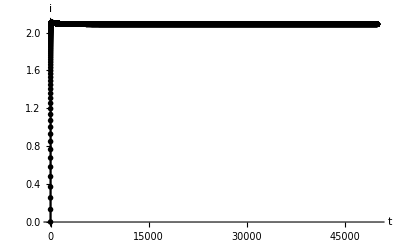

```mathematica
ListPlot[Table[{i,Y[[2,i]]},{i,1,n+1}],PlotRange->Full,Mesh->Full, Joined->True,AxesLabel->{"t","i"},PlotTheme->"Monochrome"]
```

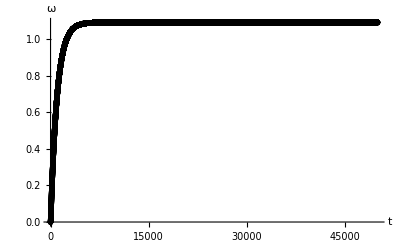

```mathematica
ListPlot[Table[{i,Y[[1,i]]},{i,1,n+1}],PlotRange->Full,Mesh->Full, Joined->True,AxesLabel->{"t","ω"},PlotTheme->"Monochrome"]
```